Numerische Berechnung von 2N+1 Windungen der Phase für konstante und kosinusförmige effektive Geschwindigkeit

```mathematica
σx=τx=PauliMatrix[1];
σy=τy=PauliMatrix[2];
σz=τz=PauliMatrix[3];
σ0=τ0=IdentityMatrix[2];
σ0τ0=KroneckerProduct[τ0,σ0];
σxτz=KroneckerProduct[τz,σx];
σyτz=KroneckerProduct[τz,σy];
σxτy=KroneckerProduct[τy,σx];
σyτy=KroneckerProduct[τy,σy];
σzτy=KroneckerProduct[τy,σz];
τx11=KroneckerProduct[τx,σ0];
τy11=KroneckerProduct[τy,σ0];
τz11=KroneckerProduct[τz,σ0];
σz11=KroneckerProduct[τ0,σz];
```

2N+1 Windung der Phase, v = const. , ϵ = ϵ0 cos(π/2m)

Matrix M erstellt. Dimension: 801x801

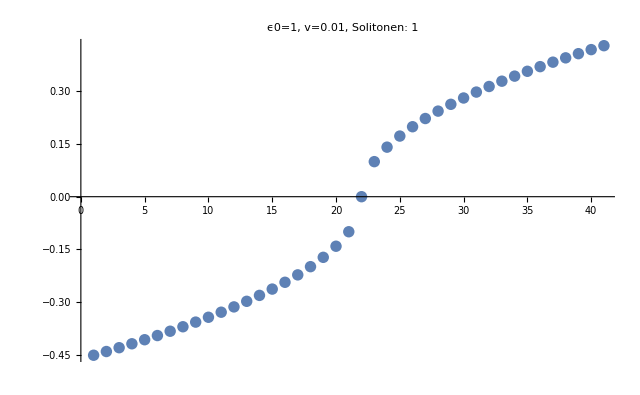

Matrix M erstellt. Dimension: 801x801

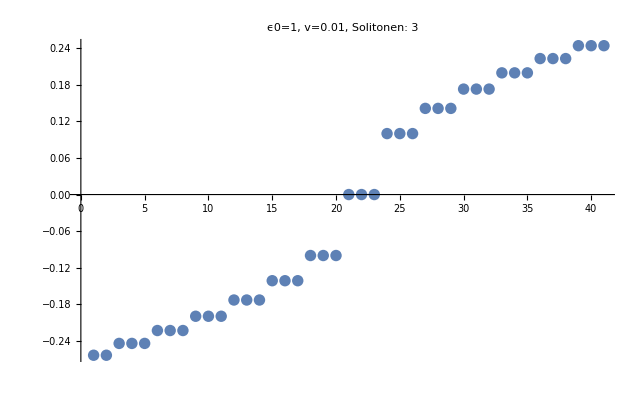

Matrix M erstellt. Dimension: 801x801

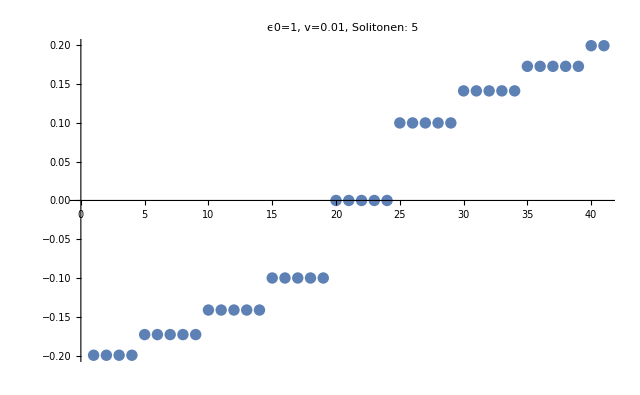

Matrix M erstellt. Dimension: 801x801

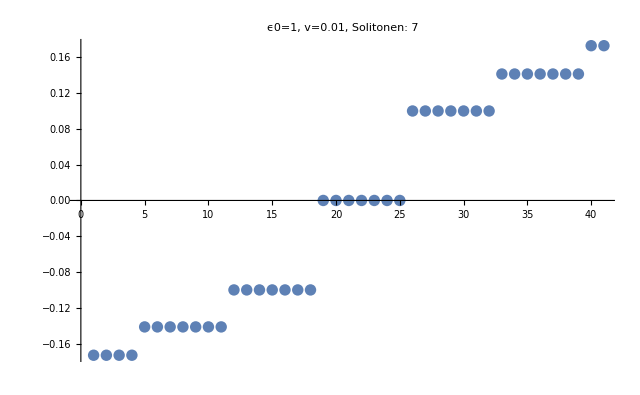

Matrix M erstellt. Dimension: 801x801

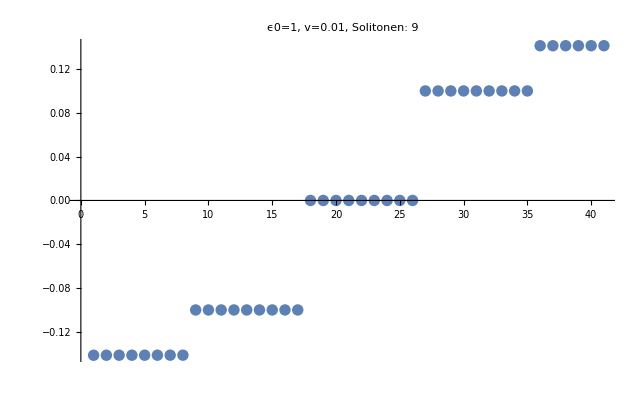

Matrix M erstellt. Dimension: 801x801

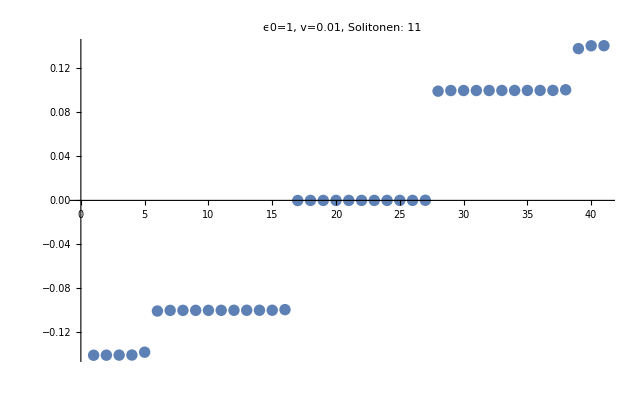

Matrix M erstellt. Dimension: 801x801

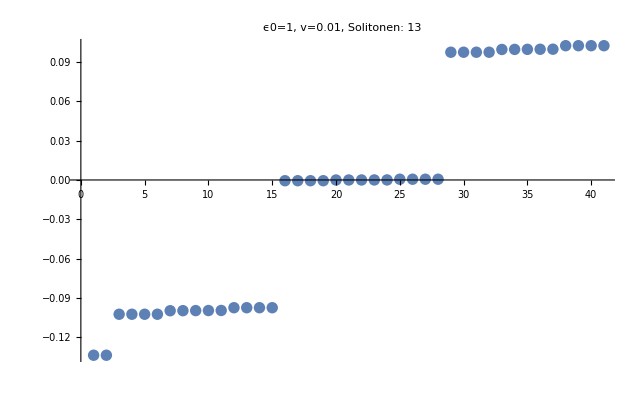

Matrix M erstellt. Dimension: 801x801

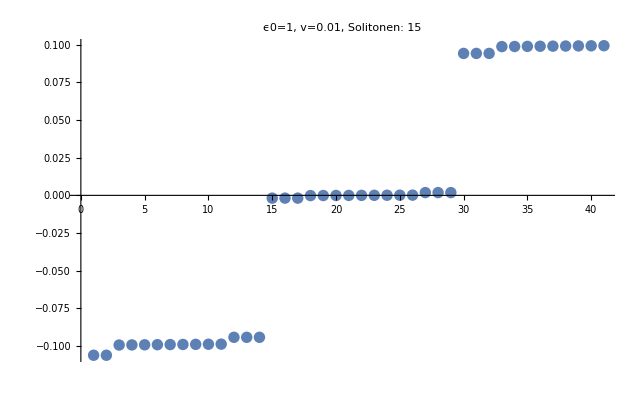

Matrix M erstellt. Dimension: 801x801

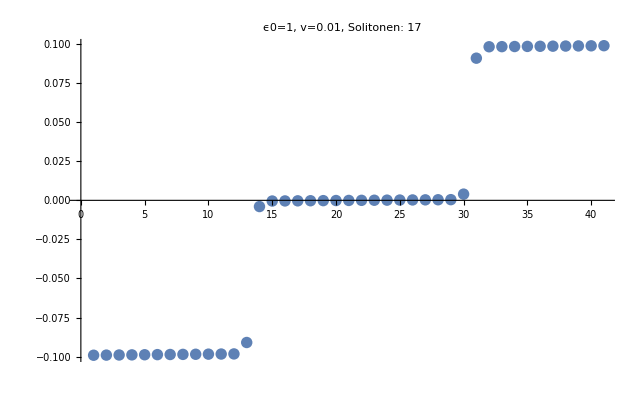

Matrix M erstellt. Dimension: 801x801

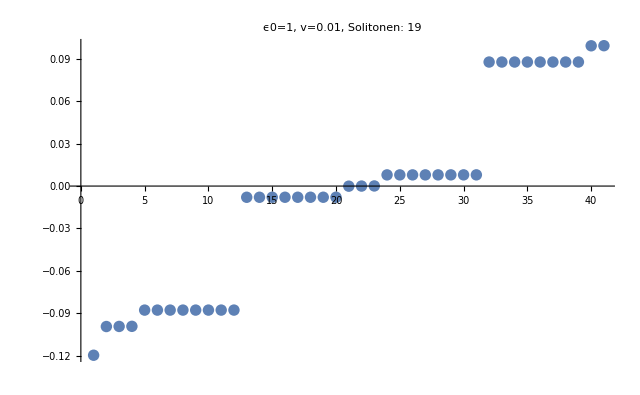

Matrix M erstellt. Dimension: 801x801

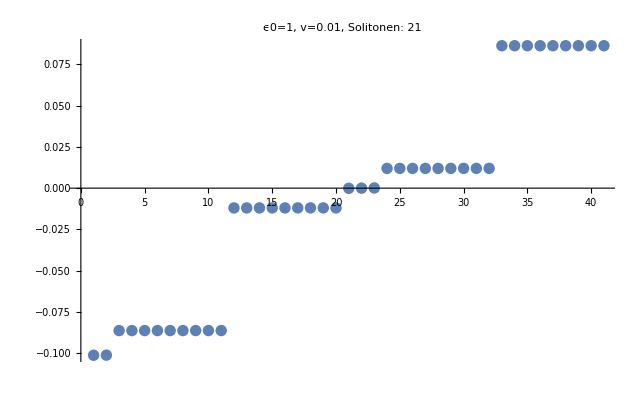

```mathematica
(*Parameter definieren*)
NSolitonenVconstMax=21;

ϵTestSingle=1;
vTestSingle=0.01;

Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];

For[i=0,(2i+1)<=NSolitonenVconstMax,i++,NSolitonen=2i+1;
M=ConstantArray[0,{dim,dim}];

m=NSolitonen;(*ϵ - Terme*)
Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/(2NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];
MatrixForm[M];
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
Print[ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"ϵ0="<>ToString[ϵTestSingle]<>", v="<> ToString[vTestSingle]<>", Solitonen: "<>ToString[NSolitonen]](*[[380;;420]]*)]
]
```

Matrix M erstellt. Dimension: 801x801

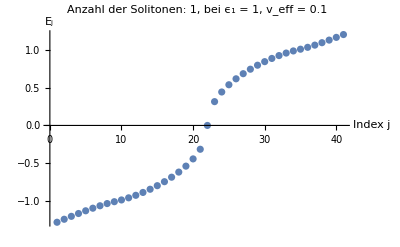

Matrix M erstellt. Dimension: 801x801

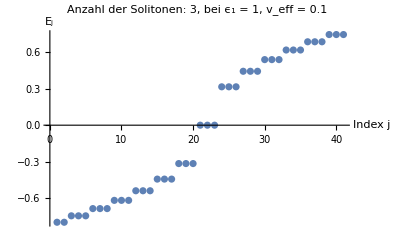

Matrix M erstellt. Dimension: 801x801

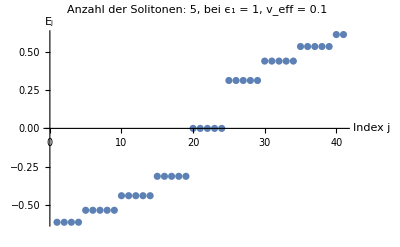

Matrix M erstellt. Dimension: 801x801

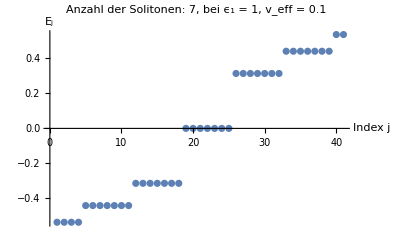

```mathematica
ϵTestSingle=1;
vTestSingle=0.1;

Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];
Plots={};

NSolitonenList={1,3,5,7};

For [i=1,i<=Length[NSolitonenList],i++,
M=ConstantArray[0,{dim,dim}];
NSolitonen=NSolitonenList[[i]];
m=NSolitonen;(*ϵ - Terme*)
Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/(2NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
plot=ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<> ToString[vTestSingle],AxesLabel->{"Index j","E_j"}];
AppendTo[Plots,plot];
Print[plot]
]
(*GraphicsRow[Plots,ImageSize->Full]*)
```

Matrix M erstellt. Dimension: 801x801

-Graphics-

Matrix M erstellt. Dimension: 801x801

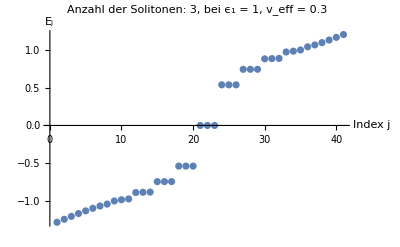

Matrix M erstellt. Dimension: 801x801

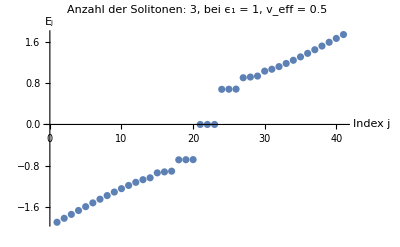

Matrix M erstellt. Dimension: 801x801

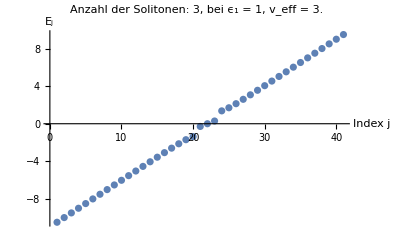

```mathematica
ϵTestSingle=1;
vTestSingle={0.1,0.3,0.5,2.9999};

Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];
Plots={};

NSolitonenList={3};

For [i=1,i<=Length[vTestSingle],i++,
M=ConstantArray[0,{dim,dim}];
NSolitonen=NSolitonenList[[1]];
m=NSolitonen;(*ϵ - Terme*)
Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/(2NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle[[i]]}];
plot=ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<> ToString[Round[vTestSingle[[i]],0.01]],AxesLabel->{"Index j","E_j"}];
AppendTo[Plots,plot];
Print[plot]
]
```

Matrix M erstellt. Dimension: 801x801

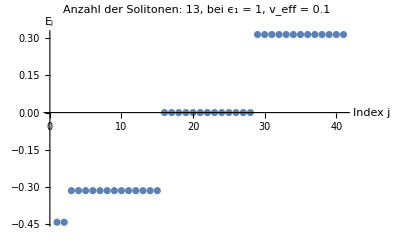

Matrix M erstellt. Dimension: 801x801

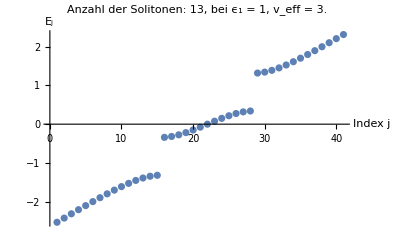

```mathematica
ϵTestSingle=1;
vTestSingle={0.1,2.999};

Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];
Plots={};

NSolitonenList={13};

For [i=1,i<=Length[vTestSingle],i++,
M=ConstantArray[0,{dim,dim}];
NSolitonen=NSolitonenList[[1]];
m=NSolitonen;(*ϵ - Terme*)
Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/(2NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle[[i]]}];
plot=ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<> ToString[Round[vTestSingle[[i]],0.01]],AxesLabel->{"Index j","E_j"}];
AppendTo[Plots,plot];
Print[plot]
]
```

Wellenfunktionen test

Matrix M erstellt. Dimension: 801x801

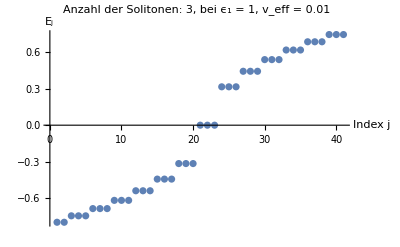

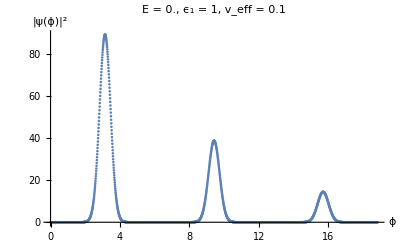

```mathematica
ϵTests={1};
vTests={0.1};

positions={400};





Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];
Plots={};

NSolitonenList={3};

For [i=1,i<=Length[NSolitonenList],i++,
NSolitonen=NSolitonenList[[i]];
m=NSolitonen;(*ϵ - Terme*)
Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/(2NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];




PsiPlots={};
For[j=1,j<=Length[vTests],j++,
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTests[[j]],v->vTests[[j]]}];
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle1,NeigvecsSingle1}],First]];
EPlot=ListPlot[sortedNeigvalsSingle[[380;;420]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<> ToString[vTestSingle],AxesLabel->{"Index j","E_j"}];
Print[EPlot];

PsiPlotsRow={};
For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/(2 NSolitonen) ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];
ψ3=Total[sortedNeigvecsSingle[[pos+2]]*vector1];
ψ4=Total[sortedNeigvecsSingle[[pos+2]]*vector1*vector2];
ψ5=Total[sortedNeigvecsSingle[[pos+1]]*vector1];
ψ6=Total[sortedNeigvecsSingle[[pos+1]]*vector1*vector2];
phase=E^(I Pi/1000);
phase2=E^(I 2Pi/3);
phase2=E^(I 7Pi/13);
ψp={+ψ1*phase2-ψ3*phase-ψ5,+ψ2*phase2-ψ4*phase-ψ6};
ψ=Conjugate[ψp].ψp;
(*ψ=Conjugate[{ψ1,ψ2}].{ψ1,ψ2};*)
PsiPlot=ListPlot[
Table[{ϕ,Re[ψ]},{ϕ,0,6Pi,0.01}],

PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTests[[j]]]<>", v_eff = "<>ToString[vTests[[j]]]];
AppendTo[PsiPlotsRow,PsiPlot];
Print[PsiPlot]
];
AppendTo[PsiPlots,PsiPlotsRow];
(*Print[GraphicsRow[PsiPlotsRow,ImageSize->Full]]*)
]
]
```

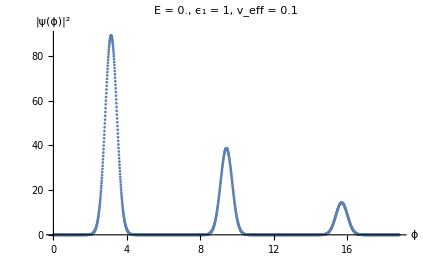

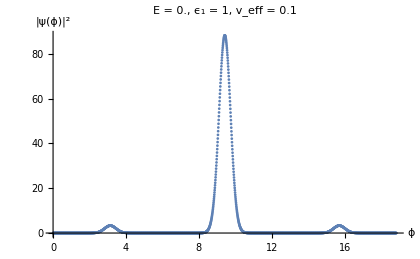

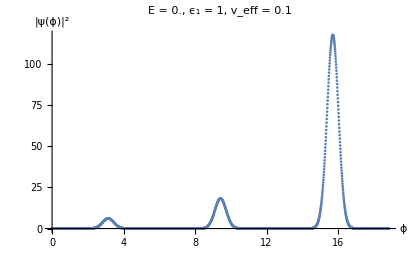

Matrix M erstellt. Dimension: 801x801

-Graphics-

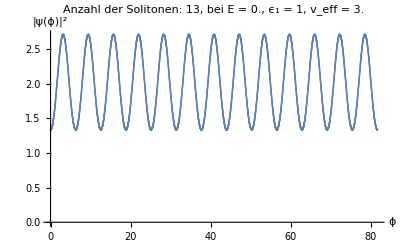

```mathematica
ϵTests={1};
vTests={2.999};

positions={401};





Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];
Plots={};

NSolitonenList={13};

For [i=1,i<=Length[NSolitonenList],i++,
NSolitonen=NSolitonenList[[i]];
m=NSolitonen;(*ϵ - Terme*)
Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/(2NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];




PsiPlots={};
For[j=1,j<=Length[vTests],j++,
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTests[[j]],v->vTests[[j]]}];
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle1,NeigvecsSingle1}],First]];
EPlot=ListPlot[sortedNeigvalsSingle[[380;;420]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<>ToString[Round[vTests[[j]],0.01]],AxesLabel->{"Index j","E_j"}];
Print[EPlot];

PsiPlotsRow={};
For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/(2 NSolitonen) ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];

ψp={ψ1,ψ2};
ψ=Conjugate[ψp].ψp;
(*ψ=Conjugate[{ψ1,ψ2}].{ψ1,ψ2};*)
PsiPlot=ListPlot[
Table[{ϕ,Re[ψ]},{ϕ,0,2 NSolitonen Pi,0.01}],

PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTests[[j]]]<>", v_eff = "<>ToString[Round[vTests[[j]],0.01]]];
AppendTo[PsiPlotsRow,PsiPlot];
Print[PsiPlot]
];
AppendTo[PsiPlots,PsiPlotsRow];
(*Print[GraphicsRow[PsiPlotsRow,ImageSize->Full]]*)
]
]
```

Matrix M erstellt. Dimension: 801x801

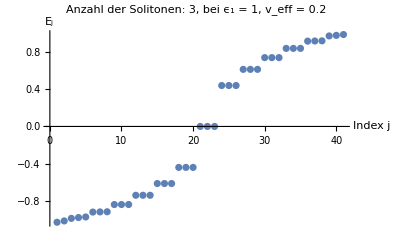

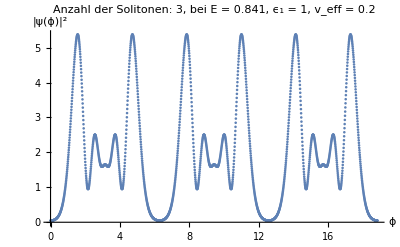

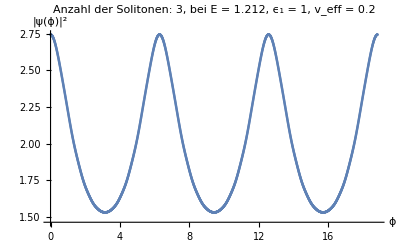

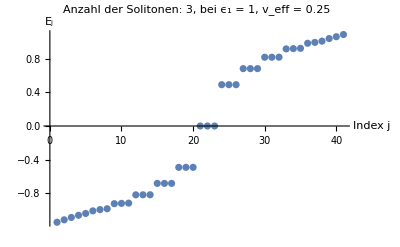

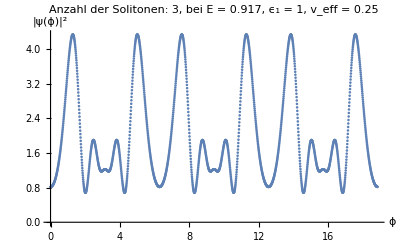

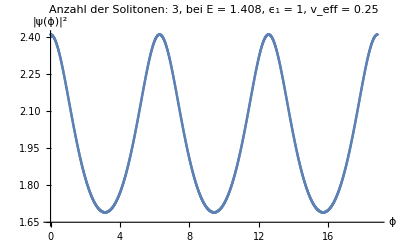

```mathematica
ϵTests={1,1};
vTests={0.2,0.25};

positions={412,430};





Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];
Plots={};

NSolitonenList={3};

For [i=1,i<=Length[NSolitonenList],i++,
NSolitonen=NSolitonenList[[i]];
m=NSolitonen;(*ϵ - Terme*)
Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/(2NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];




PsiPlots={};
For[j=1,j<=Length[vTests],j++,
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTests[[j]],v->vTests[[j]]}];
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle1,NeigvecsSingle1}],First]];
EPlot=ListPlot[sortedNeigvalsSingle[[380;;420]],
PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<>ToString[Round[vTests[[j]],0.01]],AxesLabel->{"Index j","E_j"}];
Print[EPlot];

PsiPlotsRow={};
For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/(2 NSolitonen) ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];

ψp={ψ1,ψ2};
ψ=Conjugate[ψp].ψp;
(*ψ=Conjugate[{ψ1,ψ2}].{ψ1,ψ2};*)
PsiPlot=ListPlot[
Table[{ϕ,Re[ψ]},{ϕ,0,2 NSolitonen Pi,0.01}],

PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"Anzahl der Solitonen: "<>ToString[NSolitonen]<>", bei E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTests[[j]]]<>", v_eff = "<>ToString[Round[vTests[[j]],0.01]]];
AppendTo[PsiPlotsRow,PsiPlot];
Print[PsiPlot]
];
AppendTo[PsiPlots,PsiPlotsRow];
(*Print[GraphicsRow[PsiPlotsRow,ImageSize->Full]]*)
]
]
```

2N+1 Windung der Phase, v = v0 + v1 cos(π/2mv)  , ϵ = ϵ0 cos(π/2mϵ)

Matrix M erstellt. 1-Solitonen. Dimension: 801x801

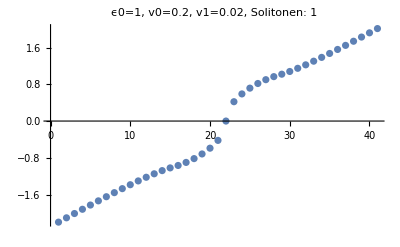

Matrix M erstellt. 3-Solitonen. Dimension: 801x801

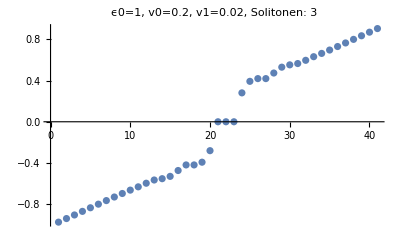

Matrix M erstellt. 5-Solitonen. Dimension: 801x801

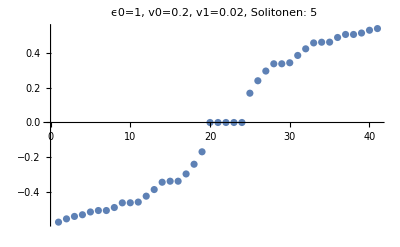

Matrix M erstellt. 7-Solitonen. Dimension: 801x801

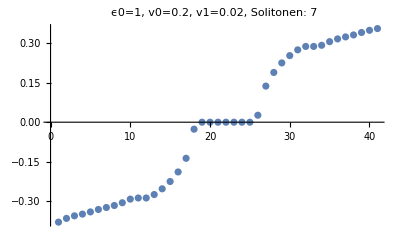

Matrix M erstellt. 9-Solitonen. Dimension: 801x801

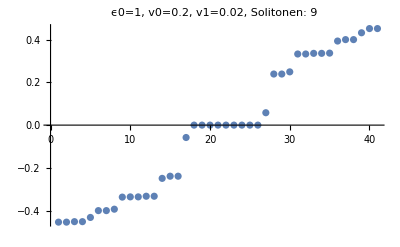

Matrix M erstellt. 11-Solitonen. Dimension: 801x801

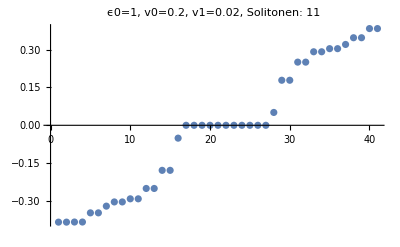

Matrix M erstellt. 13-Solitonen. Dimension: 801x801

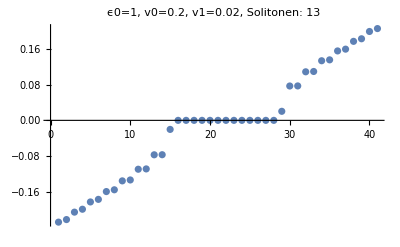

Matrix M erstellt. 15-Solitonen. Dimension: 801x801

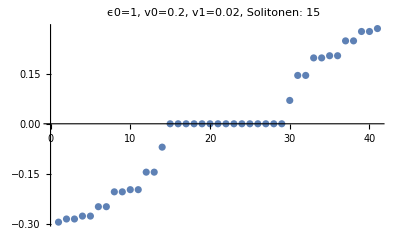

Matrix M erstellt. 17-Solitonen. Dimension: 801x801

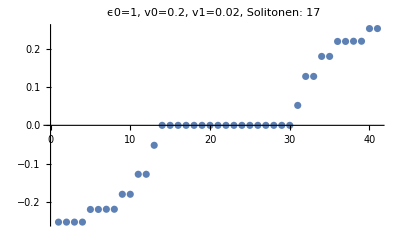

Matrix M erstellt. 19-Solitonen. Dimension: 801x801

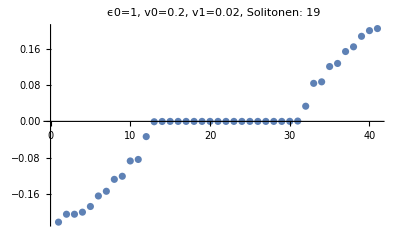

Matrix M erstellt. 21-Solitonen. Dimension: 801x801

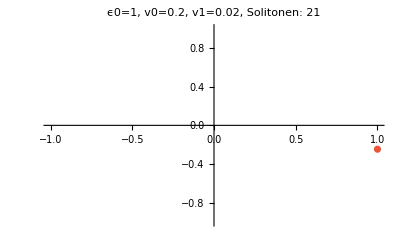

```mathematica
(*Parameter definieren*)
NSolitonenMax=21;

Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)

ϵ0TestSingle=1;
v0TestSingle=0.2;
v1TestSingle=0.02;




dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];

For[i=0,(2i+1)<=NSolitonenMax,i++,NSolitonen=2i+1;

m=2*NSolitonen;(*v_ef- Terme*)
l=NSolitonen;(*ϵ - Terme*)

Do[n=k-Ntrunc-1;
(*Diagonalelement:a_{n}*)
M[[k,k]]=-v0*n/(2 NSolitonen)*(-1)^n;
(*Off-Diagonale:a_{n+l} *)
indexPlusL=k+l;
If[1<=indexPlusL<=dim,M[[k,indexPlusL]]=ϵ0/2];
(*Off-Diagonale:a_{n-l}*)
indexMinusL=k-l;
If[1<=indexMinusL<=dim,M[[k,indexMinusL]]=ϵ0/2  ];
(*Off-Diagonale:a_{n+m} *)
indexPlusM=k+m;
If[1<=indexPlusM<=dim,M[[k,indexPlusM]]=-1/(4 NSolitonen) (-1)^(n+m) (n+m+m/2) v1];
(*Off-Diagonale:a_{n-m} *)
indexMinusM=k-m;
If[1<=indexMinusM<=dim,M[[k,indexMinusM]]=-1/(4 NSolitonen) (-1)^(n-m) (n-m-m/2) v1],
{k,1,dim}];

Print["Matrix M erstellt. ", NSolitonen,"-Solitonen. Dimension: ",dim,"x",dim];
MatrixForm[M];
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[M/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
Print[ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"ϵ0="<>ToString[ϵ0TestSingle]<>", v0="<> ToString[v0TestSingle]<>", v1="<> ToString[v1TestSingle]<>", Solitonen: "<>ToString[NSolitonen]]]
]
```